```mathematica
Clear["Global`*"]
```

```mathematica
y[x_,α_,k_]:=(Tan[α]+(m g)/(k v Cos[α])) x+g (m/k)^2 Log[1-(k x)/(m v Cos[α])]
values={v->100,m->1,g->9.81};
```

```mathematica
(* 2.1 *)
(* We are only interested in solutions with R>0, as the projectile is moving forward from x=0. *)
(* For k->0 (no friction) we get an upper bound for R: *)
rWithoutFriction[α_]=x/.Solve[Limit[y[x,α,k],k->0]==0,x][[2]]//TrigReduce
```

(v^2 Sin[2 α])/g

```mathematica
(* y[x] should be real, so the argument of the logarithm should be >0. This gives another upper bound for R: *)
rMax[α_,k_]=x/.Solve[1-(k x)/(m v Cos[α])==0,x][[1]]
```

(m v Cos[α])/k

```mathematica
(* 2.2 *)
(* If k=0 calculate the exact solution, otherwise use FindRoot with a starting point near to the maximal value of R (to ensure not to find the solution R=0). *)
range[α_,k_]:=If[k==0,
rWithoutFriction[α]/.values,
x/.FindRoot[
y[x,α,k]/.values,
{x,.99 Min[rWithoutFriction[α],rMax[α,k]]/.values,
0,Min[rWithoutFriction[α],rMax[α,k]]/.values}
]
]
```

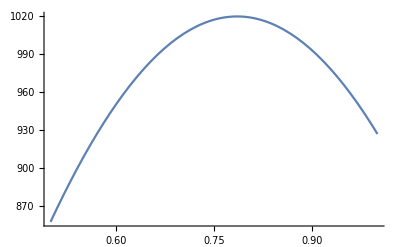

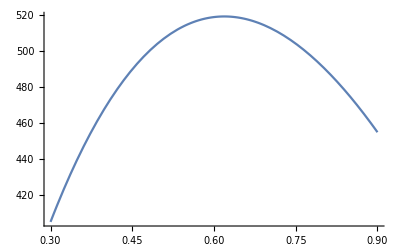

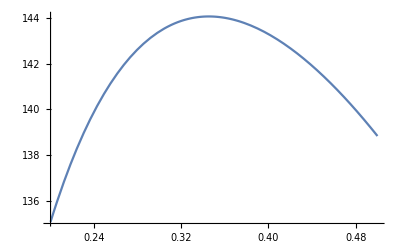

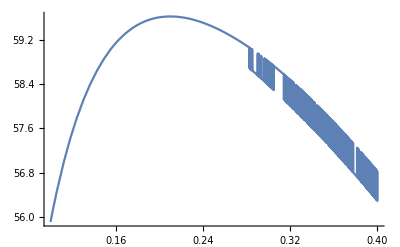

```mathematica
(* Plots of R(α) illustrating the interval to search after a maximum. *)
Plot[range[α,0],{α,.5,1.}]
Plot[range[α,.1],{α,.3,.9}]
Plot[range[α,.62],{α,.2,.5}]
Plot[range[α,1.62],{α,.1,.4}]
```

```mathematica
(* 3 *)
(* Exact solution for k=0: *)
(α/.Solve[D[rWithoutFriction[α],α]==0&&α∈Interval[{0,Pi/2}],α])[[1,1]]
```

π/4

```mathematica
(* Otherwise use FindMaximum in the intervals specified by the plots in 2.2: *)
Quiet[FindMaximum[range[α,.1],{α,.6,.5,.7}]]
Quiet[FindMaximum[range[α,.62],{α,.35,.3,.4}]]
Quiet[FindMaximum[range[α,1.62],{α,.2,.15,.25}]]
```

{519.095,{α→0.618897}}

{144.059,{α→0.345244}}

{59.6215,{α→0.209885}}